# Roots

## Open Methods

Miles Hill

## Initialization

```mathematica
Needs["NumericalMethods`"]
Needs["SchoolDisplay`"]
```

## Homework #1 ( 2015 )

### 6.19 Determine Frequency for Given Impedence

The figure shows a circuit with a resistor, an inductor, and a capacitor in parallel. Kirchoff’s rules can be used to express the impedance of the system as

1/Z=√(1/R^2+( ω C - 1/(ω L))^2)

where Z = impedance(Ω), and ω is the angular frequency.

Find ω that results in an impedance of 100Ω using the fzero function with initial guesses of 1 and 10^3 for the given parameters.
R,C,L = 225Ω, 0.6 10e-6 F, 0.5 H

To determine the angular frequency that will result in the desired impedance, the equation is first set equal to zero and then plotted over a large ranges of positive values. The visual inspection shows that a value on the upper side of ω==200 will yield the desired impedance.

#### Plot

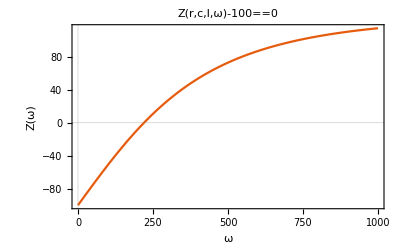

```mathematica
$Line=0;
Z[r_,c_,l_]:=(1/r^2+(# c-1/(# l))^2)^(-1/2)&
Plot[ Evaluate[ Z[225., 0.6 10^-6,0.5][ω]-100],{ω,0,1000},
FrameLabel->{"ω","Z(ω)"},
PlotTheme->"Scientific",PlotLabel->HoldForm[Z[r,c,l,ω]-100==0] ]
```

#### Code

```mathematica
(* Builit in function solutions *)
f =Z[225.,0.6 10^(-6),0.5]@#-100&;
args={f,{0.01,1000.}};
```

```mathematica
NSolve[f@ω==0 && 1.0<ω<1000.,ω,Reals][[1]];
```

```mathematica
FindRoot[f@ω,{ω,1},AccuracyGoal->5,PrecisionGoal->6];
```

```mathematica
(* Numerical methods *)
Bisection @@ args;
```

```mathematica
FalsePosition @@ args;
```

#### Output

```mathematica
DisplayColumn["Problem 6.19",{"NSolve","FindRoot","Bisection","FalsePosition"},{ω/.Out[5],ω/.Out[6],Out[7],Out[8]}]
```

NSolve
220.02
FindRoot
220.02
Bisection
220.711
FalsePosition
220.02Problem 6.19

### 6.21 Projectile Motion

The trajectory of an object defined by the xy-coordinates can be modeled by the given equation. Find the appropriate initial angle θ_0 if v_0=30 m/s and the horizontal distance is Δx =90m. Note that the initial elevation and final elevation are y_0,y_f=1.8,1.0 meters.

y=(tanθ_0)x-g/(2 v_0^2 cos^2 θ_0)x^2+y_0

As a first visual inspection of the function, the trajectory is plotted with the given values and θ_0∈[.4,.1]. From the graph its clear that two angles exists as solutions to the equation. The two intervals will be assumed to take the values ℐ_1,ℐ_2=[.5,.7],[.8,1.] .

#### Roots

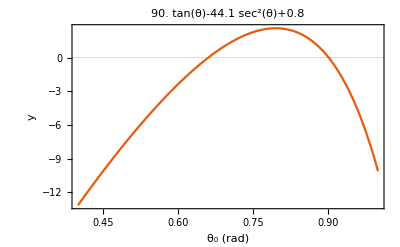

```mathematica
$Line=0;
Traj[θ0_,Δx_:90.,v0_:30.,Δy_:-0.8,g_:9.8]:=Tan[θ0]Δx-g/(2v0^2Cos[θ0]^2)Δx^2-Δy;

Plot[  Traj[x],{x,.4,1.},PlotTheme->"Scientific",FrameLabel->{"θ_0 (rad)", "y"},PlotLabel->Traj[θ]]
```

#### Code

```mathematica
(* Bisection *)
(180/Pi)(Bisection @@ {Traj,##})&/@{{0.5,0.7},{0.8,1.}};
```

```mathematica
(* FalsePosition *)
(180/Pi)(FalsePosition @@ {Traj,##})&/@{{0.5,0.7},{0.8,1.}};
```

#### OutPlot

```mathematica
(* Constants *)
With[{v0=30.,x=90.,Δy=-0.8,g=9.8},
Block[{Traj,θ0,sol},
(* Equation to solve *)
Traj[d_]:=Tan[θ0]d-g/(2v0^2Cos[θ0]^2)d^2-Δy;
(* Restricting domain of Subscript[θ, 0] *)
sol=NSolve[Traj[x]==0 && 0.<θ0<Pi/2.,θ0];

(* Visual Output *)
Plot[Evaluate[{Traj[k]/.sol[[1]],
Traj[k]/.sol[[2]]
}],{k,0.,90.},

FrameLabel->{{"y(x) [m]",None},{"x [m]",None}},
PlotLabel->"Trajectories with solved roots",
PlotLegends->LineLegend[(θ0/.sol)(180./Pi),LegendLabel->"θ_0",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
PlotStyle->{Default,Dashed},
PlotTheme->"Detailed",
Epilog->{Red,PointSize[0.03],Point[{0,1.8}],Point[{x,1.}]}
]

]];
```

#### Output

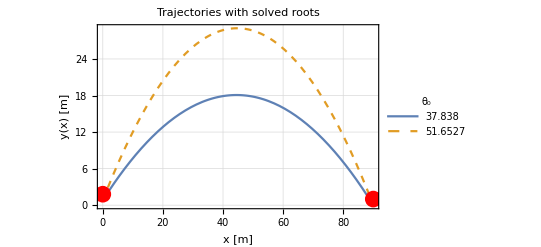
Bisection
{37.8465,51.6333}
FalsePosition
{37.838,51.6441}
Trajectories
-Graphics-Problem 6.21

```mathematica
DisplayColumn["Problem 6.21",{"Bisection","FalsePosition","Trajectories"},{Out[3],Out[4],Out[5]}]
```

### 6.29 Best Method for Root Solving

Determine the best method for root determination of the given equation. Perform iterations until the approximate relative error falls below 2%.

f(x)= 5 - 5x-ℯ^(0.5 x)

```mathematica
(* Initial conditions BRACKETING *)
{x[l],x[u]}={0.,2.};
(* NewtonRaphson & Modified Secant *)
x[i]=0.7;
```

0.7

```mathematica
(* Given function *)
f=5.-5.#-Exp[0.5 #]&;
```

```mathematica
(* Testing the methods *)
b=Bisection[f,{x[l],x[u]},MaxSteps->#]&/@Range[2,10];
fp=FalsePosition[f,{x[l],x[u]},MaxSteps->#]&/@Range[2,10];
nr=NewtonRaphson[f,x[i]];
```

```mathematica
(* Relative Error *)
RELerror[x_List,error_]:=Position[Differences[x],k_/;Abs[k]<error,1,1][[1,1]]
```

```mathematica
Grid[
Transpose[{{Bisection,FalsePosition,NewtonRaphson},RELerror[#,0.02]&/@{b,fp,nr}}]//Prepend[#,{"Method","Iter"}]&,
Frame->All,Spacings->{1, 1},Alignment->Left,Background->{None,{Pink}}]
```

Method | Iter
Bisection | 6
FalsePosition | 2
NewtonRaphson | 1

The number of iterations required to reach a relative error of less than 2.0% and the method name is listed above. The NewtonRaphson method, for the given equation, converges to the root most rapidly.

### Modified Secant